Grid[(0.560956 | 0.420416 | 0.445392 | 0.509633 | 0.511302 | 0.508281 | 0.518769 | 0.532244 | 0.488266 | 0.51119
0.571114 | 0.436255 | 0.446322 | 0.496438 | 0.515176 | 0.508368 | 0.497472 | 0.534752 | 0.479617 | 0.499983
0.566259 | 0.453043 | 0.462989 | 0.510685 | 0.502569 | 0.51726 | 0.473902 | 0.525568 | 0.47831 | 0.475427
0.565737 | 0.455917 | 0.451655 | 0.506936 | 0.508799 | 0.525147 | 0.49565 | 0.523911 | 0.486267 | 0.506577
0.52629 | 0.464832 | 0.444726 | 0.499853 | 0.516692 | 0.514863 | 0.514973 | 0.53469 | 0.513192 | 0.476384),Frame→All,Spacings→{2,1}]

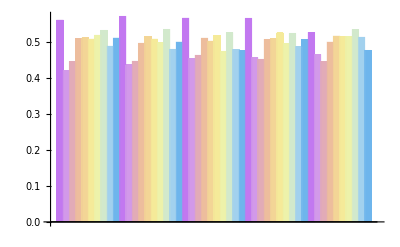

```mathematica
(*Fuzzy Logic Layer*)fuzzyLogicLayer=NetChain[{LinearLayer[10],LogisticSigmoid}];

centralGanglion=NetGraph[{"FuzzyLogic"->NetChain[{LinearLayer[10],LogisticSigmoid}],"Crosstalk"->NetMapOperator[LinearLayer[10]],"Add"->ThreadingLayer[Plus,1]  (*Adding broadcasting integer*)},{"FuzzyLogic"->"Add","Crosstalk"->"Add"->NetPort["Output"]}];

(*Updated RNN Model*)
rnnModel=NetChain[{GatedRecurrentLayer[20],LinearLayer[10]}];

(*Kohonen SOM*)
kohonenSOMLayer=NetChain[{LinearLayer[10],(*Replace with actual Kohonen logic*)LogisticSigmoid}];

(*Corrected LSTM Model*)
lstmModel=NetChain[{LongShortTermMemoryLayer[20],(*Corrected LSTM Layer*)LinearLayer[10]}];

(*Updated Generator with explicit merging of outputs*)generator=NetGraph[{"RNN"->rnnModel,"SOM"->kohonenSOMLayer,"LSTM"->lstmModel,"Catenate"->CatenateLayer[],(*Merge RNN,SOM,and LSTM outputs*)"Ganglion"->centralGanglion,"Combine"->CatenateLayer[],"FC"->LinearLayer[10]},{NetPort["Input"]->{"RNN","SOM","LSTM"},{"RNN","SOM","LSTM"}->"Catenate"->"Ganglion"->"Combine"->"FC"->NetPort["Output"]}];

(*Updated Discriminator with explicit merging of outputs*)
discriminator=NetGraph[{"RNN"->rnnModel,"SOM"->kohonenSOMLayer,"LSTM"->lstmModel,"Catenate"->CatenateLayer[],(*Merge RNN,SOM,and LSTM outputs*)"Ganglion"->centralGanglion,"Combine"->CatenateLayer[],"FC"->LinearLayer[1],"Sigmoid"->LogisticSigmoid},{NetPort["Input"]->{"RNN","SOM","LSTM"},{"RNN","SOM","LSTM"}->"Catenate"->"Ganglion"->"Combine"->"FC"->"Sigmoid"->NetPort["Output"]}];

(*Manually initialize weights and biases*)net=NetChain[{LinearLayer[10,"Weights"->RandomReal[{-0.1,0.1},{10,10}],"Biases"->RandomReal[{-0.1,0.1},{10}]],(*Manually initialized biases*)LogisticSigmoid}];

(*Input data*)
inputData=RandomReal[{0,1},{5,10}];  (*Example input:batch of 5 vectors,each with 10 elements*)

(*Evaluate the network*)
output=net[inputData];

(*Display the output*)
Grid[output//MatrixForm,Frame->All,Spacings->{2,1}]

(*Plotting each output as a bar chart*)BarChart[output,ChartLabels->Automatic,ChartStyle->"Pastel"]
```

```mathematica
%58
```

NetChain[…]